# QCD calculation: Webber et al. Sec. 7

-Graphics-

We have learned how to sum/average helicities and polarizations.
Now it’s time to handle color; you will use ColourME[].

## Two-jet cross sections (Only QCD; mass ignored) : Ellis-Stirling-Webber Sec.7.5

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (12 Mar 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

### Create Topology (and also ignore helicities)

```mathematica
topologies=CreateTopologies[0,2->2];
_Hel=0;
```

### q q' -> q q'

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SMQCD.mod

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1 aebf/cedf/ef.m, 1 diagram

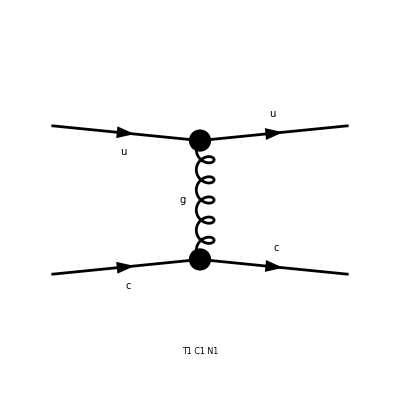

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
```

```mathematica
squared = SquaredME[amp];
helSquared=squared//.HelicityME[amp]//.{MU->0,MU2->0,MC->0,MC2->0}//Simplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

{1/4 (S^2 FF[F1 SUN1] (FFC[F1 SUN1] Mat[SUN1,SUN1]+FFC[F1 SUN2] Mat[SUN1,SUN2])+S^2 FF[F2 SUN1] (FFC[F2 SUN1] Mat[SUN1,SUN1]+FFC[F2 SUN2] Mat[SUN1,SUN2])+2 FF[F3 SUN1] ((T^2+U^2) FFC[F3 SUN1] Mat[SUN1,SUN1]+S (S+2 U) FFC[F4 SUN1] Mat[SUN1,SUN1]+((T^2+U^2) FFC[F3 SUN2]+S (S+2 U) FFC[F4 SUN2]) Mat[SUN1,SUN2])+2 FF[F4 SUN1] (S (S+2 U) FFC[F3 SUN1] Mat[SUN1,SUN1]+(T^2+U^2) FFC[F4 SUN1] Mat[SUN1,SUN1]+(S (S+2 U) FFC[F3 SUN2]+(T^2+U^2) FFC[F4 SUN2]) Mat[SUN1,SUN2])+S^2 FF[F1 SUN2] (FFC[F1 SUN1] Mat[SUN2,SUN1]+FFC[F1 SUN2] Mat[SUN2,SUN2])+S^2 FF[F2 SUN2] (FFC[F2 SUN1] Mat[SUN2,SUN1]+FFC[F2 SUN2] Mat[SUN2,SUN2])+2 FF[F3 SUN2] ((T^2+U^2) FFC[F3 SUN1] Mat[SUN2,SUN1]+S (S+2 U) FFC[F4 SUN1] Mat[SUN2,SUN1]+((T^2+U^2) FFC[F3 SUN2]+S (S+2 U) FFC[F4 SUN2]) Mat[SUN2,SUN2])+2 FF[F4 SUN2] (S (S+2 U) FFC[F3 SUN1] Mat[SUN2,SUN1]+(T^2+U^2) FFC[F4 SUN1] Mat[SUN2,SUN1]+(S (S+2 U) FFC[F3 SUN2]+(T^2+U^2) FFC[F4 SUN2]) Mat[SUN2,SUN2])),{FF[F1 SUN1]→-2 Alfas π Den[T,0],FF[F2 SUN1]→2 Alfas π Den[T,0],FF[F3 SUN1]→Alfas π Den[T,0],FF[F4 SUN1]→-Alfas π Den[T,0],FF[F1 SUN2]→2/3 Alfas π Den[T,0],FF[F2 SUN2]→-2/3 Alfas π Den[T,0],FF[F3 SUN2]→-1/3 Alfas π Den[T,0],FF[F4 SUN2]→1/3 Alfas π Den[T,0],FFC[F1 SUN1]→-2 Alfas π Den[T,0],FFC[F2 SUN1]→2 Alfas π Den[T,0],FFC[F3 SUN1]→Alfas π Den[T,0],FFC[F4 SUN1]→-Alfas π Den[T,0],FFC[F1 SUN2]→2/3 Alfas π Den[T,0],FFC[F2 SUN2]→-2/3 Alfas π Den[T,0],FFC[F3 SUN2]→-1/3 Alfas π Den[T,0],FFC[F4 SUN2]→1/3 Alfas π Den[T,0]}}

ColourME is used like HelicityME.

```mathematica
ColourME[amp]
```

{Mat[SUN1,SUN1]→9,Mat[SUN1,SUN2]→3,Mat[SUN2,SUN1]→3,Mat[SUN2,SUN2]→9}

```mathematica
helSquared//.ColourME[amp]//Simplify
```

{1/4 (3 S^2 FF[F1 SUN1] (3 FFC[F1 SUN1]+FFC[F1 SUN2])+3 S^2 FF[F1 SUN2] (FFC[F1 SUN1]+3 FFC[F1 SUN2])+3 S^2 FF[F2 SUN1] (3 FFC[F2 SUN1]+FFC[F2 SUN2])+3 S^2 FF[F2 SUN2] (FFC[F2 SUN1]+3 FFC[F2 SUN2])+6 FF[F3 SUN1] (3 (T^2+U^2) FFC[F3 SUN1]+3 S (S+2 U) FFC[F4 SUN1]+(T^2+U^2) FFC[F3 SUN2]+S (S+2 U) FFC[F4 SUN2])+2 FF[F3 SUN2] (3 (T^2+U^2) FFC[F3 SUN1]+3 S (S+2 U) FFC[F4 SUN1]+9 (T^2+U^2) FFC[F3 SUN2]+9 S (S+2 U) FFC[F4 SUN2])+6 FF[F4 SUN1] (3 S (S+2 U) FFC[F3 SUN1]+3 (T^2+U^2) FFC[F4 SUN1]+S (S+2 U) FFC[F3 SUN2]+(T^2+U^2) FFC[F4 SUN2])+2 FF[F4 SUN2] (3 S (S+2 U) FFC[F3 SUN1]+3 (T^2+U^2) FFC[F4 SUN1]+9 S (S+2 U) FFC[F3 SUN2]+9 (T^2+U^2) FFC[F4 SUN2])),{FF[F1 SUN1]→-2 Alfas π Den[T,0],FF[F2 SUN1]→2 Alfas π Den[T,0],FF[F3 SUN1]→Alfas π Den[T,0],FF[F4 SUN1]→-Alfas π Den[T,0],FF[F1 SUN2]→2/3 Alfas π Den[T,0],FF[F2 SUN2]→-2/3 Alfas π Den[T,0],FF[F3 SUN2]→-1/3 Alfas π Den[T,0],FF[F4 SUN2]→1/3 Alfas π Den[T,0],FFC[F1 SUN1]→-2 Alfas π Den[T,0],FFC[F2 SUN1]→2 Alfas π Den[T,0],FFC[F3 SUN1]→Alfas π Den[T,0],FFC[F4 SUN1]→-Alfas π Den[T,0],FFC[F1 SUN2]→2/3 Alfas π Den[T,0],FFC[F2 SUN2]→-2/3 Alfas π Den[T,0],FFC[F3 SUN2]→-1/3 Alfas π Den[T,0],FFC[F4 SUN2]→1/3 Alfas π Den[T,0]}}

```mathematica
%[[1]]//.%[[2]]//.Join[Abbr[],Subexpr[],{MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}]
FullSimplify[%/.T->-S-U]
```

1/4 ((64 Alfas2 π^2 S^2)/T^2-(6 Alfas π ((8 Alfas π S (S+2 U))/(3 T)-(8 Alfas π (T^2+U^2))/(3 T)))/T+(6 Alfas π (-(8 Alfas π S (S+2 U))/(3 T)+(8 Alfas π (T^2+U^2))/(3 T)))/T)

(16 Alfas2 π^2 (S^2+U^2))/(S+U)^2

```mathematica
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.{gs->√(4π Alfas)}]
```

(64 Alfas2 π^2 (S^2+U^2))/(9 T^2)

Now you notice that, while HelicityME takes AVARAGE, ColourME takes SUM!!!
This behavior can be summarized into two “lessons”:

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

So, in summary, we should calculate the amplitude as follows:

```mathematica
sq=SquaredME[amp]//.HelicityME[amp]//.ColourME[amp];
result=(sq[[1]]//.sq[[2]])*(2^2*(1/3)^2)//Simplify
FullSimplify[result//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}//.U->-S-T]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

32/9 Alfas2 π^2 (4 MC2^2+4 MU2^2+S^2+T^2+2 MC2 (4 MU2-S+T-U)-2 S U+U^2-2 MU2 (S-T+U)) Den[T,0]^2

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### q q' -> q q' (Again)

Let’s do it again at a stretch.

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
sq=SquaredME[amp]//.HelicityME[amp]//.ColourME[amp];
FullSimplify[(sq[[1]]//.sq[[2]])*2^2/3^2];
FullSimplify[%//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}//.U->-S-T]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1 aebf/cedf/ef.m, 1 diagram

-Graphics-

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

(2 gs^4 (T^2+(2 S+T)^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### g q -> g q

Now you can calculate all the QCD tree-level diagrams.

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 1 diagram

> Top. 2 aebf/cedf/ef.m, 1 diagram

> Top. 3 aebf/cfde/ef.m, 1 diagram

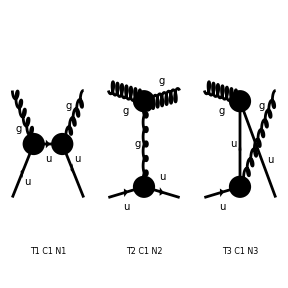

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

{FF[F3 SUN1] (16/3 (-1/2 Abb12 FFC[F1 SUN1]-1/2 Abb10 Pair2 FFC[F2 SUN1]+1/2 (-Abb16+2 MU2 Pair11 Pair2) FFC[F3 SUN1]+1/2 Abb14 FFC[F4 SUN1])-2/3 (-1/2 Abb12 FFC[F1 SUN2]-1/2 Abb10 Pair2 FFC[F2 SUN2]+1/2 (-Abb16+2 MU2 Pair11 Pair2) FFC[F3 SUN2]+1/2 Abb14 FFC[F4 SUN2]))+FF[F3 SUN2] (-2/3 (-1/2 Abb12 FFC[F1 SUN1]-1/2 Abb10 Pair2 FFC[F2 SUN1]+1/2 (-Abb16+2 MU2 Pair11 Pair2) FFC[F3 SUN1]+1/2 Abb14 FFC[F4 SUN1])+16/3 (-1/2 Abb12 FFC[F1 SUN2]-1/2 Abb10 Pair2 FFC[F2 SUN2]+1/2 (-Abb16+2 MU2 Pair11 Pair2) FFC[F3 SUN2]+1/2 Abb14 FFC[F4 SUN2]))+FF[F4 SUN1] (16/3 (1/2 (Abb18+2 MU2 Pair14) FFC[F1 SUN1]+1/2 (-Abb20+2 MU2 Pair2) FFC[F2 SUN1]+1/2 Abb22 FFC[F3 SUN1]+1/2 (-Abb19-2 MU2) FFC[F4 SUN1])-2/3 (1/2 (Abb18+2 MU2 Pair14) FFC[F1 SUN2]+1/2 (-Abb20+2 MU2 Pair2) FFC[F2 SUN2]+1/2 Abb22 FFC[F3 SUN2]+1/2 (-Abb19-2 MU2) FFC[F4 SUN2]))+FF[F4 SUN2] (-2/3 (1/2 (Abb18+2 MU2 Pair14) FFC[F1 SUN1]+1/2 (-Abb20+2 MU2 Pair2) FFC[F2 SUN1]+1/2 Abb22 FFC[F3 SUN1]+1/2 (-Abb19-2 MU2) FFC[F4 SUN1])+16/3 (1/2 (Abb18+2 MU2 Pair14) FFC[F1 SUN2]+1/2 (-Abb20+2 MU2 Pair2) FFC[F2 SUN2]+1/2 Abb22 FFC[F3 SUN2]+1/2 (-Abb19-2 MU2) FFC[F4 SUN2]))+FF[F2 SUN1] (16/3 (-1/2 Abb8 FFC[F1 SUN1]-1/2 (MU2-S) (MU2-U) FFC[F2 SUN1]-1/2 Abb6 Pair11 FFC[F3 SUN1]+1/2 (-Abb9+2 MU2 Pair11) FFC[F4 SUN1])-2/3 (-1/2 Abb8 FFC[F1 SUN2]-1/2 (MU2-S) (MU2-U) FFC[F2 SUN2]-1/2 Abb6 Pair11 FFC[F3 SUN2]+1/2 (-Abb9+2 MU2 Pair11) FFC[F4 SUN2]))+FF[F2 SUN2] (-2/3 (-1/2 Abb8 FFC[F1 SUN1]-1/2 (MU2-S) (MU2-U) FFC[F2 SUN1]-1/2 Abb6 Pair11 FFC[F3 SUN1]+1/2 (-Abb9+2 MU2 Pair11) FFC[F4 SUN1])+16/3 (-1/2 Abb8 FFC[F1 SUN2]-1/2 (MU2-S) (MU2-U) FFC[F2 SUN2]-1/2 Abb6 Pair11 FFC[F3 SUN2]+1/2 (-Abb9+2 MU2 Pair11) FFC[F4 SUN2]))+FF[F1 SUN1] (16/3 (1/2 (-Abb1-2 MU2) FFC[F1 SUN1]-1/2 Abb4 FFC[F2 SUN1]-1/2 Abb7 FFC[F3 SUN1]+1/2 (Abb3+2 MU2 Pair8) FFC[F4 SUN1])-2/3 (1/2 (-Abb1-2 MU2) FFC[F1 SUN2]-1/2 Abb4 FFC[F2 SUN2]-1/2 Abb7 FFC[F3 SUN2]+1/2 (Abb3+2 MU2 Pair8) FFC[F4 SUN2]))+FF[F1 SUN2] (-2/3 (1/2 (-Abb1-2 MU2) FFC[F1 SUN1]-1/2 Abb4 FFC[F2 SUN1]-1/2 Abb7 FFC[F3 SUN1]+1/2 (Abb3+2 MU2 Pair8) FFC[F4 SUN1])+16/3 (1/2 (-Abb1-2 MU2) FFC[F1 SUN2]-1/2 Abb4 FFC[F2 SUN2]-1/2 Abb7 FFC[F3 SUN2]+1/2 (Abb3+2 MU2 Pair8) FFC[F4 SUN2])),{FF[F1 SUN1]→Alfas Pair2 π (8 Den[T,0]+4 Den[U,MU2]),FF[F2 SUN1]→-Alfas Pair1 π (8 Den[T,0]+4 Den[U,MU2]),FF[F3 SUN1]→4 Alfas π Den[U,MU2],FF[F4 SUN1]→Alfas π (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2]),FF[F1 SUN2]→-Alfas Pair2 π (4 Den[S,MU2]+8 Den[T,0]),FF[F2 SUN2]→Alfas Pair1 π (4 Den[S,MU2]+8 Den[T,0]),FF[F3 SUN2]→4 Alfas π Den[S,MU2],FF[F4 SUN2]→-8 Alfas π (Pair3 Den[S,MU2]+Pair4 Den[T,0]),FFC[F1 SUN1]→Alfas π Pair2^* (8 Den[T,0]+4 Den[U,MU2]),FFC[F2 SUN1]→-Alfas π Pair1^* (8 Den[T,0]+4 Den[U,MU2]),FFC[F3 SUN1]→4 Alfas π Den[U,MU2],FFC[F4 SUN1]→Alfas π (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2]),FFC[F1 SUN2]→-Alfas π Pair2^* (4 Den[S,MU2]+8 Den[T,0]),FFC[F2 SUN2]→Alfas π Pair1^* (4 Den[S,MU2]+8 Den[T,0]),FFC[F3 SUN2]→4 Alfas π Den[S,MU2],FFC[F4 SUN2]→-8 Alfas π (Pair3^* Den[S,MU2]+Pair4^* Den[T,0])}}

```mathematica
diag=InsertFields[topologies,{V[5],F[3,{1}]}->{V[5],F[3,{1}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
sqHelCol=SquaredME[amp]//.HelicityME[amp]//.ColourME[amp]
```

Now do PolarizationSum. As we want to take an average (the sum) over initial (final) photon, we divide the result by 2.
With the helicity factor 2 and color factor (1/3)×(1/8), the result is given by

```mathematica
MyResult=1/2*2*1/24*PolarizationSum[sqHelCol,GaugeTerms->False]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}//FullSimplify
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)//FullSimplify
```

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

(gs^4 (36 S^4 U (T+U)-8 T^2 U^3 (T+U)+S^2 T^2 (8 T^2-7 T U+2 U^2)+S T U^2 (8 T^2+11 T U+27 U^2)+S^3 (8 T^3+5 T^2 U+45 T U^2-36 U^3)))/(36 S^2 T^2 U^2)

1/9 gs^4 (9/T^2-4/(S U)) (S^2+U^2)

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

We used GaugeTerms→False, because we know the diagram set is gauge-independent.
We can calculate with GaugeTerms and check that the result is independent of eta.
Let’s do it.

```mathematica
MyResultWithGaugeTerms=1/2*2*1/24*PolarizationSum[sqHelCol,GaugeTerms->True]//.Subexpr[]//.Abbr[]//.Den[p2_,m2_]:>1/(p2-m2)
```

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

-1/24 3
 |  |  |  |

```mathematica
MyResultWithGaugeTerms//.MU2->(S+T+U)/2//Simplify
```

(8 Alfas2 π^2 (Pair[eta[1],k[1]] (T (9 S^5+18 T^5+S^4 (62 T-27 U)+17 T^4 U-86 T^3 U^2-90 T^2 U^3+4 T U^4+9 U^5+2 S^3 (T^2-149 T U+9 U^2)-2 S^2 (8 T^3+39 T^2 U-207 T U^2-9 U^3)+S (53 T^4+162 T^3 U+166 T^2 U^2-182 T U^3-27 U^4)) Pair[eta[3],k[1]]-T (-18 S^5+3 S^4 (T+24 U)+S^3 (15 T^2+149 T U-108 U^2)+S^2 (-11 T^3+48 T^2 U-313 T U^2+72 U^3)+S (3 T^4-91 T^3 U-125 T^2 U^2+167 T U^3-18 U^4)+2 T (4 T^4+17 T^3 U+47 T^2 U^2+31 T U^3-3 U^4)) Pair[eta[3],k[2]]+9 S^6 Pair[eta[3],k[3]]+18 S^5 T Pair[eta[3],k[3]]-8 S^4 T^2 Pair[eta[3],k[3]]-25 S^3 T^3 Pair[eta[3],k[3]]-56 S^2 T^4 Pair[eta[3],k[3]]-121 S T^5 Pair[eta[3],k[3]]-73 T^6 Pair[eta[3],k[3]]-54 S^5 U Pair[eta[3],k[3]]-36 S^4 T U Pair[eta[3],k[3]]+65 S^3 T^2 U Pair[eta[3],k[3]]+114 S^2 T^3 U Pair[eta[3],k[3]]-97 S T^4 U Pair[eta[3],k[3]]-84 T^5 U Pair[eta[3],k[3]]+135 S^4 U^2 Pair[eta[3],k[3]]-36 S^3 T U^2 Pair[eta[3],k[3]]-55 S^2 T^2 U^2 Pair[eta[3],k[3]]-137 S T^3 U^2 Pair[eta[3],k[3]]+13 T^4 U^2 Pair[eta[3],k[3]]-180 S^3 U^3 Pair[eta[3],k[3]]+144 S^2 T U^3 Pair[eta[3],k[3]]-53 S T^2 U^3 Pair[eta[3],k[3]]+48 T^3 U^3 Pair[eta[3],k[3]]+135 S^2 U^4 Pair[eta[3],k[3]]-126 S T U^4 Pair[eta[3],k[3]]+51 T^2 U^4 Pair[eta[3],k[3]]-54 S U^5 Pair[eta[3],k[3]]+36 T U^5 Pair[eta[3],k[3]]+9 U^6 Pair[eta[3],k[3]]-18 S^5 T Pair[eta[3],k[4]]-6 S^4 T^2 Pair[eta[3],k[4]]+124 S^3 T^3 Pair[eta[3],k[4]]+126 S^2 T^4 Pair[eta[3],k[4]]+22 S T^5 Pair[eta[3],k[4]]+8 T^6 Pair[eta[3],k[4]]+72 S^4 T U Pair[eta[3],k[4]]+135 S^3 T^2 U Pair[eta[3],k[4]]-137 S^2 T^3 U Pair[eta[3],k[4]]-91 S T^4 U Pair[eta[3],k[4]]+33 T^5 U Pair[eta[3],k[4]]-108 S^3 T U^2 Pair[eta[3],k[4]]-165 S^2 T^2 U^2 Pair[eta[3],k[4]]-50 S T^3 U^2 Pair[eta[3],k[4]]+T^4 U^2 Pair[eta[3],k[4]]+72 S^2 T U^3 Pair[eta[3],k[4]]-51 S T^2 U^3 Pair[eta[3],k[4]]+63 T^3 U^3 Pair[eta[3],k[4]]-18 S T U^4 Pair[eta[3],k[4]]+87 T^2 U^4 Pair[eta[3],k[4]])+T (Pair[eta[1],k[3]] ((18 S^5-2 T^5+7 T^4 U+25 T^3 U^2+11 T^2 U^3-23 T U^4-18 U^5-3 S^4 (7 T+30 U)+S^3 (-23 T^2+90 T U+180 U^2)+S^2 (23 T^3+57 T^2 U-140 T U^2-180 U^3)+S (5 T^4-52 T^3 U-45 T^2 U^2+94 T U^3+90 U^4)) Pair[eta[3],k[1]]+(9 S^5+24 T^5+S^4 (44 T-45 U)+58 T^4 U+33 T^3 U^2-17 T^2 U^3-25 T U^4-9 U^5+S^3 (-6 T^2-59 T U+90 U^2)-S^2 (4 T^3-27 T^2 U+39 T U^2+90 U^3)+S (61 T^4+19 T^3 U-4 T^2 U^2+79 T U^3+45 U^4)) Pair[eta[3],k[2]]-9 S^5 Pair[eta[3],k[3]]+82 S^4 T Pair[eta[3],k[3]]+182 S^3 T^2 Pair[eta[3],k[3]]+160 S^2 T^3 Pair[eta[3],k[3]]+147 S T^4 Pair[eta[3],k[3]]+78 T^5 Pair[eta[3],k[3]]+45 S^4 U Pair[eta[3],k[3]]-29 S^3 T U Pair[eta[3],k[3]]-229 S^2 T^2 U Pair[eta[3],k[3]]-11 S T^3 U Pair[eta[3],k[3]]+144 T^4 U Pair[eta[3],k[3]]-90 S^3 U^2 Pair[eta[3],k[3]]-105 S^2 T U^2 Pair[eta[3],k[3]]-120 S T^2 U^2 Pair[eta[3],k[3]]+159 T^3 U^2 Pair[eta[3],k[3]]+90 S^2 U^3 Pair[eta[3],k[3]]-31 S T U^3 Pair[eta[3],k[3]]+167 T^2 U^3 Pair[eta[3],k[3]]-45 S U^4 Pair[eta[3],k[3]]+83 T U^4 Pair[eta[3],k[3]]+9 U^5 Pair[eta[3],k[3]]-9 S^5 Pair[eta[3],k[4]]-35 S^4 T Pair[eta[3],k[4]]-103 S^3 T^2 Pair[eta[3],k[4]]-133 S^2 T^3 Pair[eta[3],k[4]]-80 S T^4 Pair[eta[3],k[4]]-24 T^5 Pair[eta[3],k[4]]+45 S^4 U Pair[eta[3],k[4]]+73 S^3 T U Pair[eta[3],k[4]]+158 S^2 T^2 U Pair[eta[3],k[4]]-19 S T^3 U Pair[eta[3],k[4]]-57 T^4 U Pair[eta[3],k[4]]-90 S^3 U^2 Pair[eta[3],k[4]]-109 S^2 T U^2 Pair[eta[3],k[4]]-71 S T^2 U^2 Pair[eta[3],k[4]]+60 T^3 U^2 Pair[eta[3],k[4]]+90 S^2 U^3 Pair[eta[3],k[4]]+139 S T U^3 Pair[eta[3],k[4]]+16 T^2 U^3 Pair[eta[3],k[4]]-45 S U^4 Pair[eta[3],k[4]]-68 T U^4 Pair[eta[3],k[4]]+9 U^5 Pair[eta[3],k[4]])+Pair[eta[1],k[4]] ((9 S^5-S^4 (34 T+45 U)+S^3 (-4 T^2+89 T U+90 U^2)+S^2 (2 T^3+67 T^2 U-67 T U^2-90 U^3)+U (46 T^4+87 T^3 U+59 T^2 U^2+9 T U^3-9 U^4)+S (-37 T^4-85 T^3 U-122 T^2 U^2+3 T U^3+45 U^4)) Pair[eta[3],k[1]]+T ((31 S^4+26 T^4+S^3 (13 T-60 U)+97 T^3 U+95 T^2 U^2+31 T U^3+7 U^4+S^2 (-25 T^2+37 T U+34 U^2)+S (19 T^3-14 T^2 U-81 T U^2-12 U^3)) Pair[eta[3],k[2]]+(95 S^4+76 T^4+S^3 (163 T-28 U)+105 T^3 U+97 T^2 U^2+119 T U^3+51 U^4+S^2 (181 T^2-239 T U-178 U^2)+S (189 T^3+22 T^2 U-43 T U^2+60 U^3)) Pair[eta[3],k[3]]-2 (11 S^4+13 T^4+S^3 (61 T-37 U)+48 T^3 U+T^2 U^2+16 T U^3+50 U^4+S^2 (56 T^2-74 T U+91 U^2)+S (19 T^3-7 T^2 U-3 T U^2-115 U^3)) Pair[eta[3],k[4]]))-Pair[eta[1],k[2]] ((9 S^5-S^4 (7 T+45 U)+S^3 (9 T^2+73 T U+90 U^2)+S^2 (71 T^3+30 T^2 U-161 T U^2-90 U^3)+U (-39 T^4+68 T^3 U+80 T^2 U^2-36 T U^3-9 U^4)+S (46 T^4-123 T^3 U-119 T^2 U^2+131 T U^3+45 U^4)) Pair[eta[3],k[1]]+T (2 (29 S^4+13 T^4+S^3 (13 T-38 U)+6 T^3 U+38 T^2 U^2+26 T U^3-19 U^4+S^2 (22 T^2-30 U^2)+S (51 T^3-26 T^2 U-39 T U^2+58 U^3)) Pair[eta[3],k[2]]+2 (34 S^4+38 T^4+S^3 (75 T-6 U)+95 T^3 U+58 T^2 U^2+49 T U^3+48 U^4+S^2 (56 T^2-101 T U-42 U^2)+S (53 T^3+30 T^2 U-23 T U^2-34 U^3)) Pair[eta[3],k[3]]-(49 S^4+26 T^4+45 S^3 (3 T-2 U)+11 T^3 U-17 T^2 U^2+53 T U^3+55 U^4+S^2 (181 T^2-185 T U+88 U^2)+S (121 T^3-52 T^2 U-3 T U^2-102 U^3)) Pair[eta[3],k[4]])))))/(9 T^2 (S+T-U)^2 (-S+T+U)^2 Pair[eta[1],k[1]] Pair[eta[3],k[3]])

It seems that this amplitude depends on “eta” (i.e., gauge-dependent). However, note that, in this 2→2 process, k[1]+k[2]==k[3]+k[4]. Therefore...

```mathematica
%//.{Pair[eta_,k[2]]:>Pair[eta,k[3]]+Pair[eta,k[4]]-Pair[eta,k[1]]}//Simplify
```

1/(9 T^2 (S+T-U)^2 (-S+T+U)^2)8 Alfas2 π^2 (9 S^6+21 T^6+18 S^5 (2 T-3 U)+84 T^5 U+111 T^4 U^2+136 T^3 U^3+115 T^2 U^4+36 T U^5+9 U^6+S^4 (115 T^2-108 T U+135 U^2)+4 S^3 (34 T^3-43 T^2 U+18 T U^2-45 U^3)+S^2 (111 T^4-136 T^3 U+114 T^2 U^2+72 T U^3+135 U^4)+2 S (42 T^5+T^4 U-68 T^3 U^2-86 T^2 U^3-54 T U^4-27 U^5))

And we just have confirmed that this amplitude is gauge independent.
Needless to say, this agrees with the result in the canon.

```mathematica
FullSimplify[%==WebberResult,Assumptions->{S+T+U==2MU2,MU2==0,Alfas2==(gs^2/(4π))^2}]
```

True

## Summary of Calculation

```mathematica
Exit[];
```

```mathematica
(* SET UP *)
$Language="English";
<<FeynArts`
<<FormCalc`

(* Topology *)
topologies=CreateTopologies[0,2->2];

(* Diagram *)
diag=InsertFields[topologies,
{V[5],F[3,{1}]}->{V[5],F[3,{1}]},
InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];

Paint[diag];
```

FeynArts 3.10 (12 Mar 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SMQCD.mod

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 1 diagram

> Top. 2 aebf/cedf/ef.m, 1 diagram

> Top. 3 aebf/cfde/ef.m, 1 diagram

-Graphics-

```mathematica
(* Amplitude *)
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
squ=SquaredME[amp];

(* If contains Fermion *)
squ=squ//.HelicityME[amp]//.{Hel[_]->0}; (* or simply execute "_Hel=0" before this evaluation.*)

(* If contains Colored Particles *)
squ=squ//.ColourME[amp];

(* If contains Vector *)
rawResult = PolarizationSum[squ,GaugeTerms->False]; (* Asserting gauge invariance! *)
(* otherwise:
rawResult = squ[[1]]//.squ[[2]];
*)

(* Appropreate factors depending on the process *)
result=2*1/(3*8)*1/2*rawResult;
FullSimplify[result]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

4/9 Alfas2 π^2 (8 (10 MU2^2-S^2+S T+2 MU2 (S-2 T-U)-U (T+U)) Den[S,MU2]^2+36 (2 MU2^2-2 MU2 (S+T)+S (S+T-U)) Den[T,0]^2+9 (8 MU2^2+2 S (2 S+T)-2 MU2 (7 S+3 T)+(S+3 T) U+U^2) Den[T,0] Den[U,MU2]-8 (6 MU2^2-T (S+T)+(2 S+T) U+4 U^2-2 MU2 (2 S+T+8 U)) Den[U,MU2]^2+Den[S,MU2] (9 (12 MU2^2+2 S T-S U+T U+3 U^2-2 MU2 (4 T+7 U)) Den[T,0]+(-40 MU2^2+S (3 S+T)-3 S U+2 U^2+2 MU2 (5 S+8 T+6 U)) Den[U,MU2]))

```mathematica
MyResult=FullSimplify[%//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}]
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)
```

(gs^4 (36 S^4 U (T+U)-8 T^2 U^3 (T+U)+S^2 T^2 (8 T^2-7 T U+2 U^2)+S T U^2 (8 T^2+11 T U+27 U^2)+S^3 (8 T^3+5 T^2 U+45 T U^2-36 U^3)))/(36 S^2 T^2 U^2)

gs^4 ((S^2+U^2)/T^2-(4 (S^2+U^2))/(9 S U))

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

DIVIDE by INITIAL vector particles.